# Ellipse for H’

## (2-3) - axes for quantization

## A.M. components written in terms of the spherical coordinates

```mathematica
x1[r_,theta_,fi_]:={r Cos[theta],r Sin[theta]Sin[fi],r Sin[theta]Cos[fi]};
x2[r_,theta_,fi_]:={r Sin[theta]Cos[fi],r Cos[theta],r Sin[theta]Sin[fi]};
x3[r_,theta_,fi_]:={r Sin[theta]Sin[fi],r Sin[theta]Cos[fi],r Cos[theta]};
```

## Inertial functions

```mathematica
Afct[spin_,j_,a1_,a2_,theta_]:=a2(1-(j*Sin[theta])/spin)-a1;
ufct[spin_,j_,a1_,a2_,a3_,theta_]:=(a3-a1)/Afct[spin,j,a1,a2,theta];
v0fct[spin_,j_,a1_,a2_,theta_]:=-(a1*j*Cos[theta])/Afct[spin,j,a1,a2,theta];
vfct[spin_,j_,a1_,a2_,theta_]:=v0fct[spin,j,a1,a2,theta]/spin;
```

## The ellipse’s (a,b) coefficients

```mathematica
a[I_,E_,j_,a1_,a2_,theta_]:=((1-vfct[I,j,a1,a2,theta])/(E-2*vfct[I,j,a1,a2,theta]*I^2))^(-1/2);
b[I_,E_,j_,a1_,a2_,a3_,theta_]:=((ufct[I,j,a1,a2,a3,theta]-vfct[I,j,a1,a2,theta])/(E-2*vfct[I,j,a1,a2,theta]*I^2))^(-1/2);
```

## Inertia factors

```mathematica
A1={1/(2*38),1/(2*32)};
A2={1/(2*68),1/(2*19)};
A3={1/(2*51),1/(2*81)};
```

## Constants

```mathematica
j=5.5;
spin=9.5;
θ={110*π/180,113*π/180};
```

## Quantization picker for ellipse parameters (a,b)

```mathematica
ae[E_,I_,k_]:=a[I,E,j,A1[[k]],A2[[k]],θ[[k]]];
be[E_,I_,k_]:=b[I,E,j,A1[[k]],A2[[k]],A3[[k]],θ[[k]]];
(*ae[E_,I_,k_]:=a[I,E,j,P,Q,θ];
be[E_,I_,k_]:=b[I,E,j,P,Q,R,θ];*)
```

```mathematica
(*Manipulate[ae[e,s,1]/.{P->1/(2w1),Q->1/(2w2)},{e,0,100},{s,0.5,32.5,2},{w1,1,100,1},{w2,1,100,1}]*)
```

```mathematica
(*Manipulate[be[e,s,1]/.{P->1/(2w1),Q->1/(2w2),R->1/(2w3)},{e,0,100},{s,0.5,32.5,2},{w1,1,100,0.5},(*{w2,1,100,0.5}*),{w3,1,100,1}]*)
```

# 2-axis quantization (k=1)

## Parameter a

## 2-axis quantization

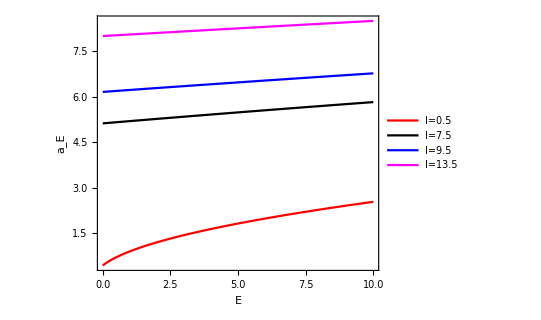

```mathematica
Plot[{ae[x,0.5,1],ae[x,7.5,1],ae[x,9.5,1],ae[x,13.5,1]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=0.5","I=7.5","I=9.5","I=13.5"},Automatic],PlotRange->Full,Epilog->Inset[Graphics[{Style[Text["ℐ_2>ℐ_3>ℐ_1"],19,Bold,Black,Italic,FontFamily->"Times New Roman"]}],Scaled[{0.2,0.4}]]]
```

## 3-axis quantization

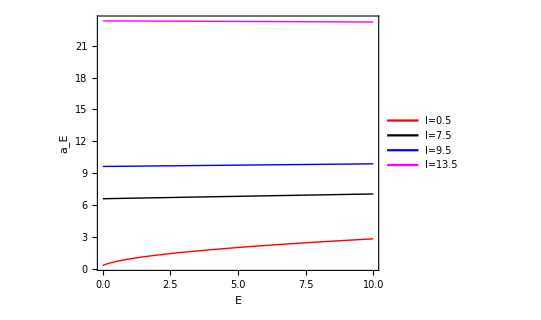

```mathematica
Plot[{ae[x,0.5,2],ae[x,7.5,2],ae[x,9.5,2],ae[x,13.5,2]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=0.5","I=7.5","I=9.5","I=13.5"},{0.2,0.70}],PlotRange->Full,Epilog->Inset[Graphics[{Style[Text["ℐ_3>ℐ_1>ℐ_2"],19,Bold,Black,Italic,FontFamily->"Times New Roman"]}],Scaled[{0.8,0.7}]]]
```

## Parameter b

### Testing 2-axis quantization

```mathematica
(*Manipulate[Plot[be[x,s,1],{x,0,100},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][s]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],{s,0.5,22.5,2}]*)
```

### Testing 3-axis quantization

```mathematica
(*Manipulate[Plot[be[x,s,2],{x,0,100},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][s]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],{s,0.5,22.5,2}]*)
```

## 2-axis quantization

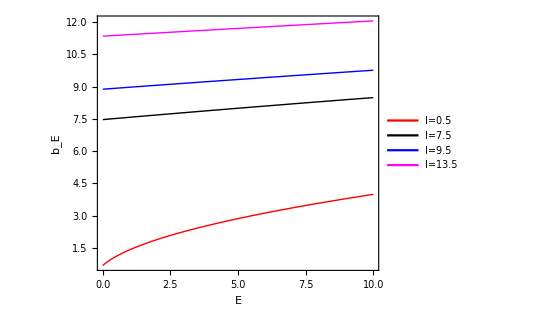

```mathematica
Plot[{be[x,0.5,1],be[x,7.5,1],be[x,9.5,1],be[x,13.5,1]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=0.5","I=7.5","I=9.5","I=13.5"},{0.77,0.28}],PlotRange->Full,Epilog->Inset[Graphics[{Style[Text["ℐ_2>ℐ_3>ℐ_1"],19,Bold,Black,Italic,FontFamily->"Times New Roman"]}],Scaled[{0.25,0.4}]]]
```

## 3-axis quantization

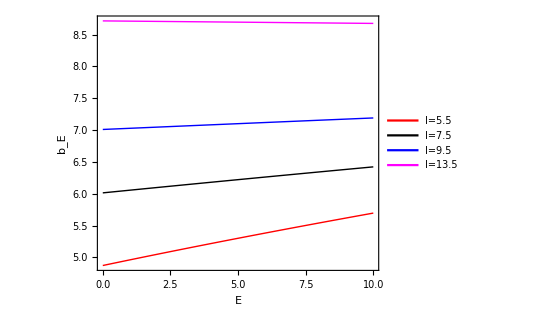

```mathematica
Plot[{be[x,5.5,2],be[x,7.5,2],be[x,9.5,2],be[x,13.5,2]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=5.5","I=7.5","I=9.5","I=13.5"},{0.75,0.68}],PlotRange->Full,Epilog->Inset[Graphics[{Style[Text["ℐ_3>ℐ_1>ℐ_2"],19,Bold,Black,Italic,FontFamily->"Times New Roman"]}],Scaled[{0.25,0.7}]]]
```

## Plot the energy ellipse H’ and the angular momentum sphere I

## Intersection points for the ellipse H’ and the am. I

```mathematica
pts[E_,I_,k_]:=NSolve[x^2/ae[E,I,k]^2+y^2/be[E,I,k]^2==1&&{x,y}∈Circle[{0,0},I],{x,y}];
intersections[E_,I_,k_]:={Black,PointSize[Large],Point[{x,y}/.pts[E,I,k]]};
parabola[E_,I_,k_]:=ContourPlot[x^2/ae[E,I,k]^2+y^2/be[E,I,k]^2==1,{x,-15,15},{y,-15,15}];
```

```mathematica
g[k_]:=  GraphicsGrid[{{Show[ContourPlot[x^2/ae[0,9.5,k]^2+y^2/be[0,9.5,k]^2==1,{x,-16,16},{y,-16,16},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,0]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}]],Show[ContourPlot[x^2/ae[15,9.5,k]^2+y^2/be[15,9.5,k]^2==1,{x,-16,16},{y,-16,16},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,15]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[15,9.5,k]}]]},{Show[ContourPlot[x^2/ae[25,9.5,k]^2+y^2/be[25,9.5,k]^2==1,{x,-16,16},{y,-16,16},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,25]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[25,9.5,k]}]],Show[ContourPlot[x^2/ae[35,9.5,k]^2+y^2/be[35,9.5,k]^2==1,{x,-16,16},{y,-16,16},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,35]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[35,9.5,k]}]]}},Frame->All];
```

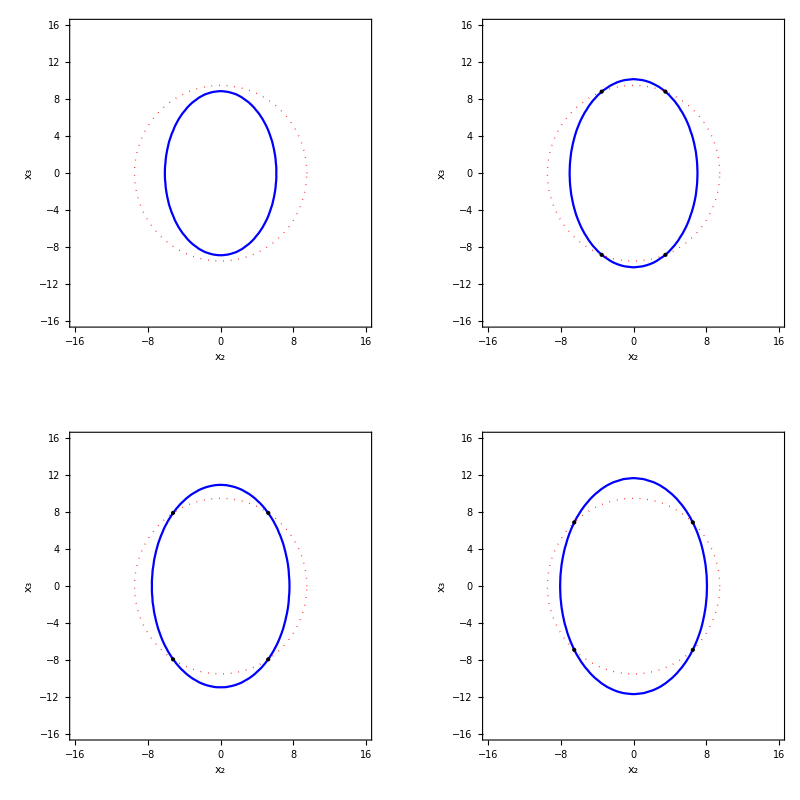

```mathematica
g[1]
```

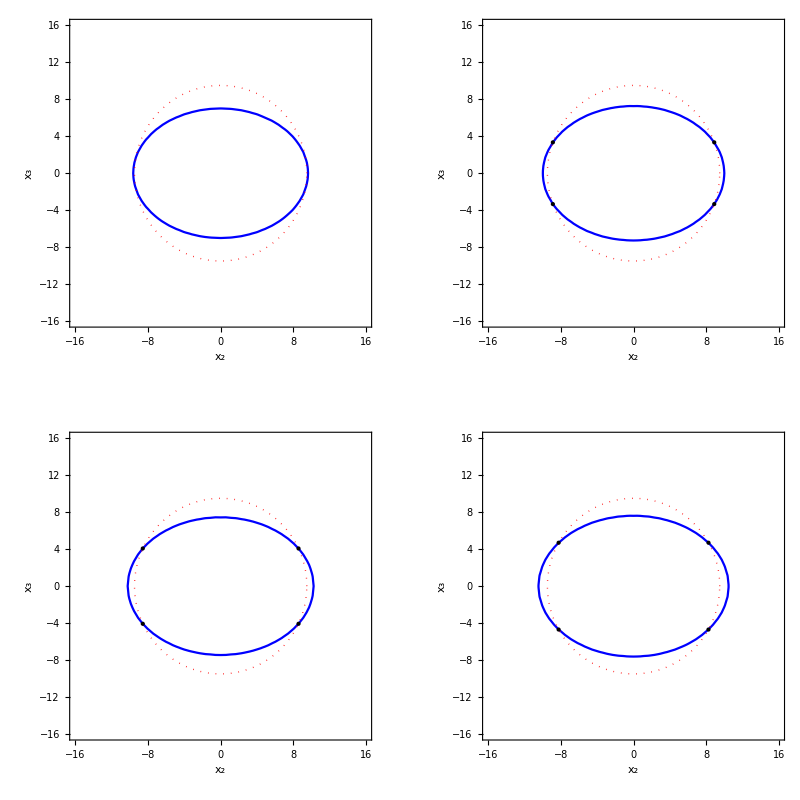

```mathematica
g[2]
```

```mathematica
Manipulate[Show[ContourPlot[((x^2/a[i,e,j,P,Q,T*π/180]^2+y^2/b[i,e,j,P,Q,R,T*π/180]^2)/.{P->1/(2w1),Q->1/(2w2),R->1/(2w3),T->unghi})==1,{x,-15,15},{y,-15,15},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][i,e]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},i]}]],{e,0,50,2},{i,2.5,12.5,1},{w1,1,100,1},{w2,1,100,1},{w3,1,100,1},{unghi,-180,180,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. (Charting`Private`pvar$4282)^2 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.